```mathematica
p=10;(*number of integration points*)
λ=500*^-9;(*wavelength*)
k=(2 π)/λ;(*wavenumber*)
NA=1.32;(*numerical aperture*)
n=1.518;(*refractive index*)
α=ArcSin[NA/n](*angular extent of aperture*)
min=-2 λ;max=2 λ;step = 200;(*transverse dimensions*)
zmin=-3 λ;zmax=3 λ;zstep=100;(*longitudinal dimensions*)
f=1 λ;(*focal length*)
l0=1;(*peak field amplitude*)
A=(π f l0)/λ;(*constant before integration*)
β=1.5;(*ratio of pupil radius to beam waist AT ENTRANCE PUPIL*)
u[z_]:=k z Sin[α]^2;(*as defined in Richards & Wolf*)
v2d = Table[{k Sin[α] √(x^2+y^2),z},{x,Range[min,max,(max-min)/step]},{y,Range[min,max,(max-min)/step]},{z,Range[zmin,zmax,(zmax-zmin)/zstep]}];
v1d=Abs[Table[{k Sin[α] Range[min,max,(max-min)/step],z},{z,Range[zmin,zmax,(zmax-zmin)/zstep]}]]; (*array with {v,z} value of each physical position*)
apod[θ_]:=Exp[-β^2 (Sin[θ]/Sin[α])^2];(* BesselJ[1,2 β Sin[θ]/Sin[α]];*)(*apodization function*)
```

1.05432

```mathematica
RHO2d=Z2d=PHI2d=0*v2d;
RHO2d[[All,All,All,2]]=Z2d[[All,All,All,2]]=PHI2d[[All,All,All,2]]=v2d[[All,All,All,2]];
RHO2d[[All,All,All,1]]=NIntegrate[√Cos[x]*Sin[2 x]*apod[x]*BesselJ[1,v2d[[All,All,All,1]] Sin[x]/Sin[α]] *Exp[I u[RHO2d[[All,All,All,2]]] Cos[x]/Sin[α]^2],{x,0,α}];
Z2d[[All,All,All,1]]=NIntegrate[√Cos[x]*Sin[x]^2*apod[x]*BesselJ[0,v2d[[All,All,All,1]] Sin[x]/Sin[α]]* Exp[I u[Z2d[[All,All,All,2]]] Cos[x]/Sin[α]^2],{x,0,α}];
```

```mathematica
RHO1d=Z1d=PHI1d=0*v1d;
```

```mathematica
RHO1d[[All,2]]=Z1d[[All,2]]=PHI1d[[All,2]]=v1d[[All,2]];
RHO1d[[All,1]]=NIntegrate[√Cos[x]*Sin[2 x]*apod[x]*BesselJ[1,v1d[[All,1]] Sin[x]/Sin[α]] *Exp[I u[RHO1d[[All,2]]] Cos[x]/Sin[α]^2],{x,0,α},Method->{"TrapezoidalRule","Points"->10}];
Z1d[[All,1]]=NIntegrate[√Cos[x]*Sin[x]^2*apod[x]*BesselJ[0,v1d[[All,1]] Sin[x]/Sin[α]]* Exp[I u[Z1d[[All,2]]] Cos[x]/Sin[α]^2],{x,0,α},Method->{"TrapezoidalRule","Points"->10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.527161}. NIntegrate obtained 0.03569+0.0211168 ⅈ and 0.000203419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.527161}. NIntegrate obtained 0.0375711+0.0199669 ⅈ and 0.00020276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.527161}. NIntegrate obtained 0.0393953+0.0187037 ⅈ and 0.000197856 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658951}. NIntegrate obtained -0.00724543+0.00649649 ⅈ and 0.0000551626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658951}. NIntegrate obtained -0.00687638+0.00703295 ⅈ and 0.0000548306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658951}. NIntegrate obtained -0.00647425+0.00753686 ⅈ and 0.0000548934 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
ArrayPlot[Abs[Transpose[RHO1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

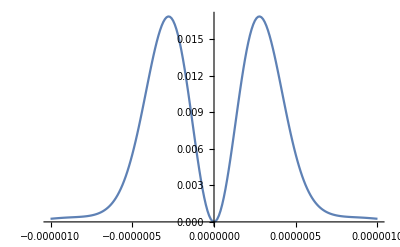

```mathematica
ListLinePlot[Abs[RHO1d[[2,1]]]^2,DataRange->{min,max},PlotRange->All]
```

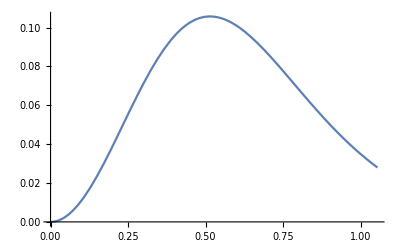

```mathematica
Plot[Abs[√Cos[x]*Sin[2 x]*apod[x]*BesselJ[1, Sin[x]/Sin[α]] *Exp[I Cos[x]/Sin[α]^2]],{x,0,α}]
```

```mathematica
ListLinePlot[v1d[[1,2]]]
```

ListLinePlot::lpn: 5.×10^-9 is not a list of numbers or pairs of numbers.

ListLinePlot[1/200000000]